```mathematica
critval=InverseCDF[ChiSquareDistribution[2],0.95]
```

5.99146

```mathematica
pval=1-CDF[ChiSquareDistribution[2],6.16]
```

0.0459593

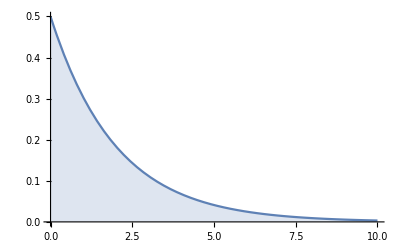

```mathematica
Plot[PDF[ChiSquareDistribution[2],x]//Evaluate,{x,0,10},Filling->Axis]
```

```mathematica
quakes=Import[NotebookDirectory[]<>"SimplifiedEarthquakeCatalog2019.txt","Table","HeaderLines"->1];
dates=quakes[[All,1]];
times=Differences[dates];
```

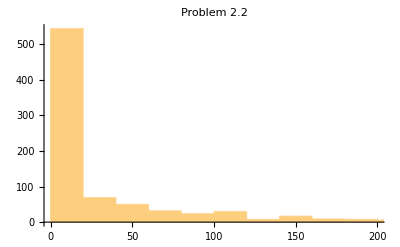

```mathematica
Histogram[times,PlotLabel->"Problem 2.2"]
```

```mathematica
Mean[N[times]]
StandardDeviation[N[times]]
```

37.8646

75.2639

```mathematica
Maximize[{Length[times]*Log[x]-x*Total[times],x≥0},x]
```

{-3832.33,{x→0.0264099}}

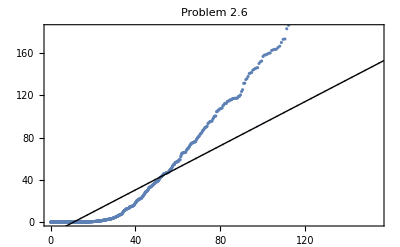

```mathematica
QuantilePlot[times,ExponentialDistribution[0.0264],PlotLabel->"Problem 2.6"]
```

```mathematica
htd=KolmogorovSmirnovTest[times,ExponentialDistribution[0.0264],"HypothesisTestData"]
htd["TestConclusion"]
htd["TestDataTable"]
```

HypothesisTestData[…]

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

The null hypothesis that the data is distributed according to the ExponentialDistribution[0.0264] is rejected at the 5 percent level based on the Kolmogorov-Smirnov test.

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

| Statistic | P-Value
Kolmogorov-Smirnov | 0.452369 | 1.91399×10^-148

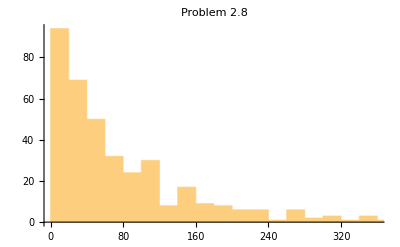

82.4699

93.6857

{-2040.49,{x→0.0121256}}

```mathematica
times2=Select[times,#>4&];
Histogram[times2,PlotLabel->"Problem 2.8"]
Mean[N[times2]]
StandardDeviation[N[times2]]
Maximize[{Length[times2]*Log[x]-x*Total[times2],x≥0},x]
```

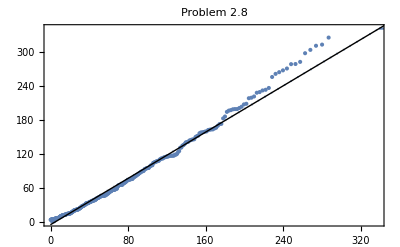

HypothesisTestData[…]

The null hypothesis that the data is distributed according to the ExponentialDistribution[0.0121] is not rejected at the 5 percent level based on the Kolmogorov-Smirnov test.

| Statistic | P-Value
Kolmogorov-Smirnov | 0.0633837 | 0.0926099

```mathematica
QuantilePlot[times2,ExponentialDistribution[0.0121],PlotLabel->"Problem 2.8"]
htd=KolmogorovSmirnovTest[times2,ExponentialDistribution[0.0121],"HypothesisTestData"]
htd["TestConclusion"]
htd["TestDataTable"]
```

```mathematica
Integrate[x*0.0121*Exp[-0.0121*x],{x,0,Infinity}]
```

82.6446

```mathematica
anscombe1=Import[NotebookDirectory[]<>"Anscombe1.txt","Table","HeaderLines"->1];
anscombe2=Import[NotebookDirectory[]<>"Anscombe2.txt","Table","HeaderLines"->1];
anscombe3=Import[NotebookDirectory[]<>"Anscombe3.txt","Table","HeaderLines"->1];
anscombe4=Import[NotebookDirectory[]<>"Anscombe4.txt","Table","HeaderLines"->1];
```

```mathematica
Mean[anscombe1]
StandardDeviation[anscombe1]
Mean[anscombe2]
StandardDeviation[anscombe2]
Mean[anscombe3]
StandardDeviation[anscombe3]
Mean[anscombe4]
StandardDeviation[anscombe4]
```

{9.,7.50091}

{3.31662,2.03157}

{9.,7.50091}

{3.31662,2.03166}

{9.,7.5}

{3.31662,2.03042}

{9.,7.50091}

{3.31662,2.03058}

FittedModel[3.00009+0.500091 x]

FittedModel[3.00091+0.5 x]

FittedModel[3.00245+0.499727 x]

FittedModel[3.00173+0.499909 x]

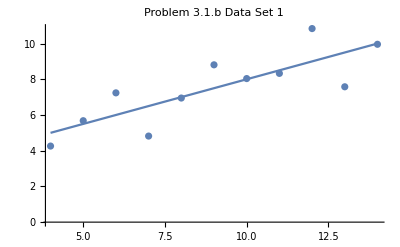

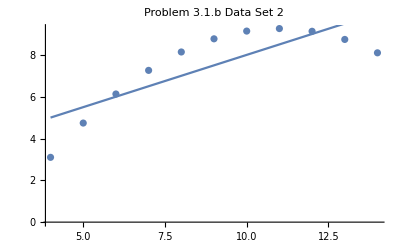

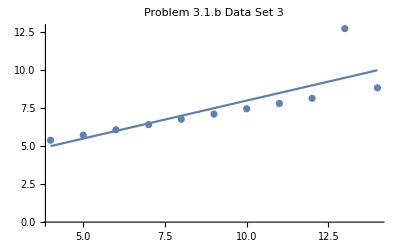

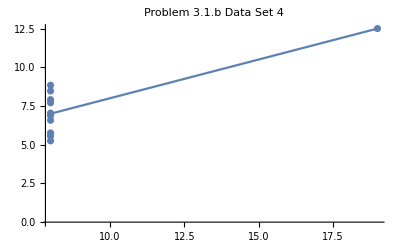

```mathematica
mod1=LinearModelFit[anscombe1,x,x]
mod2=LinearModelFit[anscombe2,x,x]
mod3=LinearModelFit[anscombe3,x,x]
mod4=LinearModelFit[anscombe4,x,x]
Show[ListPlot[anscombe1,PlotLabel->"Problem 3.1.b Data Set 1"],Plot[Normal[mod1],{x,Min[anscombe1[[All,1]]],Max[anscombe1[[All,1]]]}]]
Show[ListPlot[anscombe2,PlotLabel->"Problem 3.1.b Data Set 2"],Plot[Normal[mod2],{x,Min[anscombe2[[All,1]]],Max[anscombe2[[All,1]]]}]]
Show[ListPlot[anscombe3,PlotLabel->"Problem 3.1.b Data Set 3"],Plot[Normal[mod3],{x,Min[anscombe3[[All,1]]],Max[anscombe3[[All,1]]]}]]
Show[ListPlot[anscombe4,PlotLabel->"Problem 3.1.b Data Set 4"],Plot[Normal[mod4],{x,Min[anscombe4[[All,1]]],Max[anscombe4[[All,1]]]}]]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 3.00009 | 1.12475 | 2.66735 | 0.0257341
x | 0.500091 | 0.117906 | 4.24146 | 0.00216963

0.666542

0.629492

{17.9899}

{0.00216963}

13.7627

1.2366

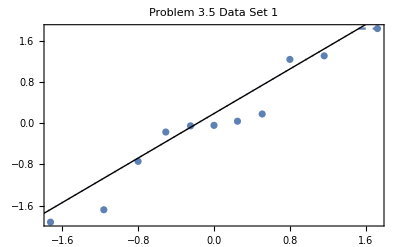

HypothesisTestData[…]

The null hypothesis that the data is distributed according to the NormalDistribution[0,1] is not rejected at the 5 percent level based on the Kolmogorov-Smirnov test.

| Statistic | P-Value
Kolmogorov-Smirnov | 0.169297 | 0.859988

```mathematica
mod1["ParameterTable"]
mod1["RSquared"]
mod1["AdjustedRSquared"]
mod1["ANOVATableFStatistics"]
mod1["ANOVATablePValues"]
e=mod1["FitResiduals"];
ssr=Total[e e]
T=Length[anscombe1];
Sqrt[ssr/(T-2)]
QuantilePlot[e,PlotLabel->"Problem 3.5 Data Set 1"]
htd=KolmogorovSmirnovTest[e/StandardDeviation[e],NormalDistribution[0,1],"HypothesisTestData"]
htd["TestConclusion"]
htd["TestDataTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 3.00091 | 1.1253 | 2.66676 | 0.0257589
x | 0.5 | 0.117964 | 4.23859 | 0.00217882

0.666242

0.629158

{17.9656}

{0.00217882}

13.7763

1.23721

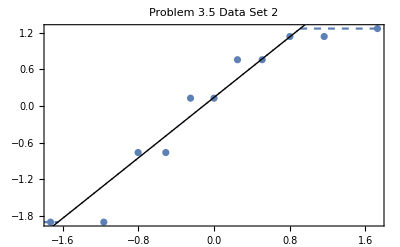

HypothesisTestData[…]

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

The null hypothesis that the data is distributed according to the NormalDistribution[0,1] is not rejected at the 5 percent level based on the Kolmogorov-Smirnov test.

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

| Statistic | P-Value
Kolmogorov-Smirnov | 0.195644 | 0.725271

```mathematica
mod2["ParameterTable"]
mod2["RSquared"]
mod2["AdjustedRSquared"]
mod2["ANOVATableFStatistics"]
mod2["ANOVATablePValues"]
e=mod2["FitResiduals"];
ssr=Total[e e]
T=Length[anscombe2];
Sqrt[ssr/(T-2)]
QuantilePlot[e,PlotLabel->"Problem 3.5 Data Set 2"]
htd=KolmogorovSmirnovTest[e/StandardDeviation[e],NormalDistribution[0,1],"HypothesisTestData"]
htd["TestConclusion"]
htd["TestDataTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 3.00245 | 1.12448 | 2.67008 | 0.0256191
x | 0.499727 | 0.117878 | 4.23937 | 0.00217631

0.666324

0.629249

{17.9723}

{0.00217631}

13.7562

1.23631

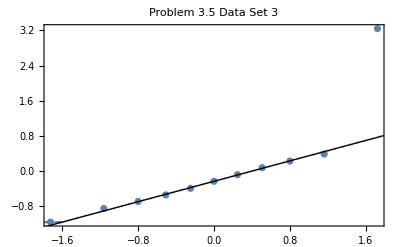

HypothesisTestData[…]

The null hypothesis that the data is distributed according to the NormalDistribution[0,1] is not rejected at the 5 percent level based on the Kolmogorov-Smirnov test.

| Statistic | P-Value
Kolmogorov-Smirnov | 0.279279 | 0.298712

```mathematica
mod3["ParameterTable"]
mod3["RSquared"]
mod3["AdjustedRSquared"]
mod3["ANOVATableFStatistics"]
mod3["ANOVATablePValues"]
e=mod3["FitResiduals"];
ssr=Total[e e]
T=Length[anscombe3];
Sqrt[ssr/(T-2)]
QuantilePlot[e,PlotLabel->"Problem 3.5 Data Set 3"]
htd=KolmogorovSmirnovTest[e/StandardDeviation[e],NormalDistribution[0,1],"HypothesisTestData"]
htd["TestConclusion"]
htd["TestDataTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 3.00173 | 1.12392 | 2.67076 | 0.0255904
x | 0.499909 | 0.117819 | 4.24303 | 0.0021646

0.666707

0.629675

{18.0033}

{0.0021646}

13.7425

1.2357

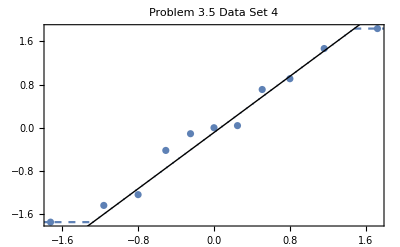

HypothesisTestData[…]

The null hypothesis that the data is distributed according to the NormalDistribution[0,1] is not rejected at the 5 percent level based on the Kolmogorov-Smirnov test.

| Statistic | P-Value
Kolmogorov-Smirnov | 0.12784 | 0.983457

```mathematica
mod4["ParameterTable"]
mod4["RSquared"]
mod4["AdjustedRSquared"]
mod4["ANOVATableFStatistics"]
mod4["ANOVATablePValues"]
e=mod4["FitResiduals"];
ssr=Total[e e]
T=Length[anscombe4];
Sqrt[ssr/(T-2)]
QuantilePlot[e,PlotLabel->"Problem 3.5 Data Set 4"]
htd=KolmogorovSmirnovTest[e/StandardDeviation[e],NormalDistribution[0,1],"HypothesisTestData"]
htd["TestConclusion"]
htd["TestDataTable"]
```

```mathematica
NormalDistribution[0,1]
```

NormalDistribution[0,1]